Math 21b Mathematica Project
Annamira O’Toole
April 24th, 2017

Problem 1
Get the Kirchhoff matrix of a Wheel graph  (WheelGraph) with 10 elements. Use the command “Normal” to see the matrix which will be given as a SparseArray.

```mathematica
Normal[KirchhoffMatrix[WheelGraph[10]]]
```

{{9,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,3,-1,0,0,0,0,0,0,-1},{-1,-1,3,-1,0,0,0,0,0,0},{-1,0,-1,3,-1,0,0,0,0,0},{-1,0,0,-1,3,-1,0,0,0,0},{-1,0,0,0,-1,3,-1,0,0,0},{-1,0,0,0,0,-1,3,-1,0,0},{-1,0,0,0,0,0,-1,3,-1,0},{-1,0,0,0,0,0,0,-1,3,-1},{-1,-1,0,0,0,0,0,0,-1,3}}

Problem 2
Find the eigenvalues of the complete graph (CompleteGraph) with 10 elements.

```mathematica
Eigenvalues[KirchhoffMatrix[CompleteGraph[10]]]
```

{10,10,10,10,10,10,10,10,10,0}

Problem 3
Find the QR decomposition of the 7x7 matrix which has entries A(i,j) =ij+1 everywhere.

```mathematica
A =  A=Table[i*j+1,{i,7},{j,7}];
QRDecomposition[A]
```

{{{2/(√203),3/(√203),4/(√203),5/(√203),6/(√203),√(7/29),8/(√203)},{-19/(2 √203),-√(7/29),-9/(2 √203),-2/(√203),1/(2 √203),3/(√203),11/(2 √203)}},{{√203,53 √(7/29),77 √(7/29),43 √(7/29)+2 √203,125 √(7/29),149 √(7/29),43 √(7/29)+5 √(29/7)+765/(√203)},{0,2 √(7/29),4 √(7/29),-(55 √(7/29))/2+(11 √(29/7))/2+75/(√203),-17 √(7/29)-4 √(29/7)+291/(√203),10 √(7/29),-19 √(7/29)-2 √(29/7)+275/(√203)}}}

Problem 4
Produce a chart of the distribution of the largest eigenvalue of a random graph with 70 vertices and edge probability 0.6

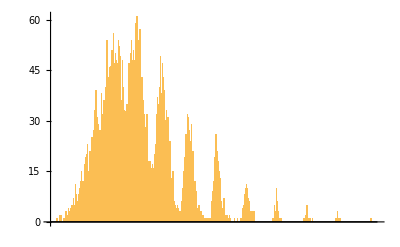

```mathematica
LargestEigenvalueRandomGraph[n_,p_]:=Max[N[Eigenvalues[1.0*KirchhoffMatrix[RandomGraph[{n,Floor[p *n*(n-1)/2]}]]]]];
BarChart[BinCounts[Table[LargestEigenvalueRandomGraph[70,0.6],{10000}],0.01]]
```

Problem 5
Find the general solution of the differential equation f’’[x]-f’[x]+f[x]==Sin[x^2]

```mathematica
ClearAll[f];S = DSolve[f''[x]-f'[x]+f[x]==Sin[x^2],f[x],x]
```

{{f[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]-1/4 (-1)^(1/4) ⅇ^(-ⅈ/8-(√3)/8+x/2) √(π/3) (ⅈ Cos[(√3 x)/2] Erfi[1/4 (-1)^(1/4) (-ⅈ+√3-4 x)]+ⅇ^(ⅈ/4) Cos[(√3 x)/2] Erfi[1/4 (-1)^(3/4) (ⅈ+√3-4 x)]+ⅇ^(ⅈ/4+(√3)/4) Cos[(√3 x)/2] Erfi[1/4 (-1)^(3/4) (-ⅈ+√3+4 x)]+ⅈ ⅇ^((√3)/4) Cos[(√3 x)/2] Erfi[1/4 (-1)^(1/4) (ⅈ+√3+4 x)]-Erfi[1/4 (-1)^(1/4) (-ⅈ+√3-4 x)] Sin[(√3 x)/2]-ⅈ ⅇ^(ⅈ/4) Erfi[1/4 (-1)^(3/4) (ⅈ+√3-4 x)] Sin[(√3 x)/2]+ⅈ ⅇ^(ⅈ/4+(√3)/4) Erfi[1/4 (-1)^(3/4) (-ⅈ+√3+4 x)] Sin[(√3 x)/2]+ⅇ^((√3)/4) Erfi[1/4 (-1)^(1/4) (ⅈ+√3+4 x)] Sin[(√3 x)/2])}}

Problem 6
Find the first 7 terms of the Fourier series of the function  f[x_]: = ArcTan[x] on [-Pi,Pi]

```mathematica
ClearAll[f,a,aa,s]
f[x_]:= ArcTan[x] on [-Pi,Pi];
a[n_]:=Integrate[(1/Pi) f[x] Sin[n x],{x,-Pi,Pi}];
aa=Table[a[k],{k,1,7}]
s[x_,n_]:=Sum[aa[[k]] Sin[k x],{k,1,n}];
```

{1/(2 ⅇ π)on[-π,π] (4 ⅇ ArcTan[π]-ⅈ CosIntegral[ⅈ-π]+ⅈ CosIntegral[ⅈ+π]-SinIntegral[ⅈ-π]+ⅇ^2 (-ⅈ CosIntegral[ⅈ-π]+ⅈ CosIntegral[ⅈ+π]+SinIntegral[ⅈ-π]-SinIntegral[ⅈ+π])+SinIntegral[ⅈ+π]),-1/(4 ⅇ^2 π)on[-π,π] (4 ⅇ^2 ArcTan[π]+ⅈ (1+ⅇ^4) (CosIntegral[2 ⅈ-2 π]-CosIntegral[2 ⅈ+2 π])+SinIntegral[2 ⅈ-2 π]-ⅇ^4 SinIntegral[2 ⅈ-2 π]-SinIntegral[2 ⅈ+2 π]+ⅇ^4 SinIntegral[2 ⅈ+2 π]),1/(6 ⅇ^3 π)on[-π,π] (4 ⅇ^3 ArcTan[π]-ⅈ CosIntegral[3 ⅈ-3 π]+ⅈ CosIntegral[3 ⅈ+3 π]-SinIntegral[3 ⅈ-3 π]+ⅇ^6 (-ⅈ CosIntegral[3 ⅈ-3 π]+ⅈ CosIntegral[3 ⅈ+3 π]+SinIntegral[3 ⅈ-3 π]-SinIntegral[3 ⅈ+3 π])+SinIntegral[3 ⅈ+3 π]),-1/(8 ⅇ^4 π)on[-π,π] (4 ⅇ^4 ArcTan[π]+ⅈ (1+ⅇ^8) (CosIntegral[4 ⅈ-4 π]-CosIntegral[4 ⅈ+4 π])+SinIntegral[4 ⅈ-4 π]-ⅇ^8 SinIntegral[4 ⅈ-4 π]-SinIntegral[4 ⅈ+4 π]+ⅇ^8 SinIntegral[4 ⅈ+4 π]),1/(10 ⅇ^5 π)on[-π,π] (4 ⅇ^5 ArcTan[π]-ⅈ CosIntegral[5 ⅈ-5 π]+ⅈ CosIntegral[5 ⅈ+5 π]-SinIntegral[5 ⅈ-5 π]+ⅇ^10 (-ⅈ CosIntegral[5 ⅈ-5 π]+ⅈ CosIntegral[5 ⅈ+5 π]+SinIntegral[5 ⅈ-5 π]-SinIntegral[5 ⅈ+5 π])+SinIntegral[5 ⅈ+5 π]),-1/(12 ⅇ^6 π)on[-π,π] (4 ⅇ^6 ArcTan[π]+ⅈ (1+ⅇ^12) (CosIntegral[6 ⅈ-6 π]-CosIntegral[6 ⅈ+6 π])+SinIntegral[6 ⅈ-6 π]-ⅇ^12 SinIntegral[6 ⅈ-6 π]-SinIntegral[6 ⅈ+6 π]+ⅇ^12 SinIntegral[6 ⅈ+6 π]),1/(14 ⅇ^7 π)on[-π,π] (4 ⅇ^7 ArcTan[π]-ⅈ CosIntegral[7 ⅈ-7 π]+ⅈ CosIntegral[7 ⅈ+7 π]-SinIntegral[7 ⅈ-7 π]+ⅇ^14 (-ⅈ CosIntegral[7 ⅈ-7 π]+ⅈ CosIntegral[7 ⅈ+7 π]+SinIntegral[7 ⅈ-7 π]-SinIntegral[7 ⅈ+7 π])+SinIntegral[7 ⅈ+7 π])}

Problem 7
Fit the primes data=Table[{k,N[Prime[k]/k]},{k,100000}]; with functions {1,x,Log[x]}. The result will be a function which suggests the prime number theorem.

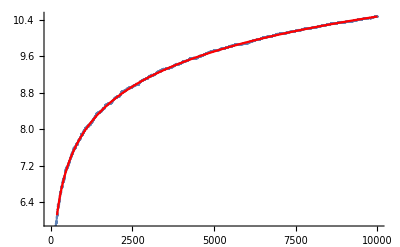

```mathematica
h[x_]:=x+2*Random[];M=10000;
data=Table[{k,N[Prime[k]/k]},{k,10000}]; 
f=Fit[data,{1,x,Log[x]},x];
S1=ListPlot[data];
S2=Plot[f,{x,0,10000},PlotStyle->{Red}];
Show[{S1,S2}]
```

Problem 8
Use the Poem generator to make a small poem. You can modify the poem afterwards. Just use the generator as an idea machine.

```mathematica
ClearAll["Global`*"];
Adjectives={orthogonal, orthonormal, complicated, difficult, fascinating, beautiful, focused };
Adverbs={desperately,passionately,slowly,softly,carefully,tenderly,gently,quickly,kindly};
Articles={the,a}; Ditverbs={finished,transformed,solved, sketched}; Spronouns={Kant, Hobbes, Nietzsche, Hume, Plato, Aristotle, Socrates, Locke, Descartes, Sartre, Rousseau};
Opronouns=Nouns;
Itverbs={reduced, found, integrated, solved, factored, projected};
Nouns={eigenvalue, eigenfunction, eigenvector, matrix, nonlinear system, dynamical system, basis, image, kernel, transformation, determinant, problem, homework, Kant, Hobbes, Nietzsche, Plato, Aristotle, Socrates,Hume, Locke, Descartes, Sartre, Rousseau, Fourier series}, nullclines, the Jacobian;
Preps={from,for,with} ;Pronouns={Kant, Hobbes, Nietzsche, Plato, Aristotle, Socrates,Hume, Locke, Descartes, Sartre, Rousseau};
Tverbs={loved,hated,talked to,glared at,greeted, calculated, stumped};
Verbs={multiplied, reduced, integrated, solved, factored, projected};

Print["Famous philosophers find new pastimes in Heaven: a poem"]

Adjective:=RandomChoice[Adjectives];Adverb:=RandomChoice[Adverbs];Ditverb:=RandomChoice[Ditverbs];
Itverb:=RandomChoice[Itverbs];Noun:=RandomChoice[Nouns];Opronoun:=RandomChoice[Opronouns];
Prep:=RandomChoice[Preps];Pronoun:=RandomChoice[Pronouns];Spronoun:=RandomChoice[Spronouns];
OPronoun:=RandomChoice[Opronouns];Tverb:=RandomChoice[Tverbs];Verb:=RandomChoice[Verbs];
Article=RandomChoice[Articles]; Subject:=RandomChoice[{{Article,Noun},{Spronoun},{Article,Adjective,Noun}}];
Predicatelist:={{Adverb},{Prep,Article,Adjective,Noun},{Prep,Opronoun},{Article,Adjective,Noun},
{Opronoun},{Article,Adjective,Noun,Adverb},{Opronoun,Adverb},{Opronoun,Article,Adjective,Noun}};
Verblist:={{Itverb},{Itverb},{Itverb},{Tverb},{Tverb},{Tverb},{Tverb},{Ditverb}};
Predicate:=RandomChoice[Table[{Verblist[[i]],Predicatelist[[i]]},{i,Length[Verblist]}]];
Object:=RandomChoice[{{},{Adverb},{Subject},{Opronoun},{Prepsubject}}];
Verbobject:={Verb,Object}; Prepsubject:={Prep,Subject}; Subjectpredicate:={Subject,Predicate};
Continuations:=If[Length[Object]+Length[Prep]<4,{"and",Subjectpredicate},{}];
Sentence:=Flatten[RandomChoice[{{Subject,Verbobject}}]];Verse:=Table[Sentence,{5}];
Poem=Table[Verse,{3}];
Do[V=Poem[[j]];Do[S=V[[k]];Do[W=S[[m]];If[m==1,W=Capitalize[ToString[W]]]; WriteString["poem.txt",W," "],{m,Length[S]}];WriteString["poem.txt","\n"],{k,Length[V]-1}];WriteString["poem.txt","\n"],{j,Length[Poem]}]; Close["poem.txt"];
A=Import["poem.txt"]
```

Famous philosophers find new pastimes in Heaven: a poem

Sartre multiplied a transformation 
A focused Nietzsche factored a dynamical system 
Aristotle integrated with a eigenfunction 
Hobbes solved softly

Plato projected from a orthogonal kernel 
A fascinating Locke worked with a Nietzsche 
Rousseau found nullclines of a dynamical system 
Locke calculated a Fourier series 

A beautiful Socrates solved for Rousseau 
Kant loved a complicated nonlinear system
Descartes found the Jacobian 
Nietzsche gently derived

Famous philosophers find new pastimes in Heaven: a poem
(edited a little bit for grammar)

Locke multiplied matrices with Nietzsche 
A majestic orthonormal eigenbasis was discovered 
An orthogonal matrix multiplied
Aristotle had an epiphany

An eigenfunction factored slowly 
Kant sketched a dynamical system 
Descartes row-reduced kindly 
Rousseau projected carefully 

Hume calculated a determinant
A majestic transformation factored carefully 
A difficult eigenfunction multiplied 
Socrates finished his homework

An eigenvector multiplied 
A matrix projected a difficult image
A focused Sartre integrated a nonlinear system
Plato factored passionately

```mathematica
"Sartre multiplied a transformation \nA focused Nietzsche factored a dynamical system \nAristotle integrated with a eigenfunction \nHobbes solved softly\n\nPlato projected from a orthogonal kernel \nA fascinating Locke worked with a Nietzsche \nRousseau found nullclines of a dynamical system \nLocke calculated a Fourier series \n\nA beautiful Socrates solved for Rousseau \nKant loved a complicated nonlinear system\nDescartes found the Jacobian \nNietzsche gently derived\n"
```